# Narciso Cluster Analysis

### Using Mathematica to investigate variations in samples from Porto

## Header

### Standard Header Section

```mathematica
Needs["HierarchicalClustering`"]
Needs["ProteomicsAnalysis`"]
Needs["ManualPCA`"]
Needs["PrincipalComponentsVariance`"]
Needs["VennDiagram`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\Andrew\Porto_iTRAQ

```mathematica
FileNames[]
```

{13211_iTRAQ2-pepts.xls,13211_iTRAQ2-quants.xls,13212_iTRAQ1-pepts.xls,13212_iTRAQ1-PHENYX.xls,13212_iTRAQ1-quants.xls,porto_iTRAQ1-EASYPROT.xlsx,porto_iTRAQ1.nb,porto_iTRAQ1_peptide-data.csv,Porto_PCA_iTRAQ1.pdf,Porto_PCA_iTRAQ2.pdf,ProteomicsAnalysis.m}

## Peptide investigation

### Import data

```mathematica
rawPeptideData1=Import["13212_iTRAQ1-pepts.xls"][[1]];
rawPeptideData2=Import["13211_iTRAQ2-pepts.xls"][[1]];
Dimensions[rawPeptideData1]
Dimensions[rawPeptideData2]
```

{8000,20}

{14815,20}

### Putting the data into a workable format

```mathematica
heads=rawPeptideData1[[1,All]];
workingPeptideData1=rawPeptideData1[[2;;All,All]];
workingPeptideData2=rawPeptideData2[[2;;All,All]];
```

```mathematica
heads[[11;;18]]
labelIntensities1=workingPeptideData1[[All,11;;18]];
labelIntensities2=workingPeptideData2[[All,11;;18]];
```

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

### Removing empty rows and null intensity data

```mathematica
noSpaceIntensities1=Pick[labelIntensities1,#,False]&[Thread[workingPeptideData1[[All,1]]==""]];
noSpaceIntensities2=Pick[labelIntensities2,#,False]&[Thread[workingPeptideData2[[All,1]]==""]];
```

```mathematica
sanitisedPeptides1=noSpaceIntensities1/.""->0.;
sanitisedPeptides2=noSpaceIntensities2/.""->0.;
```

### Normalising the data

```mathematica
Table[Total[sanitisedPeptides1[[All,i]]],{i,8}]
Table[Total[sanitisedPeptides2[[All,i]]],{i,8}]
```

{6876.62,6125.97,5659.23,6833.95,6678.35,5251.11,5762.09,5380.86}

{14755.3,12179.7,12547.4,12265.7,15007.9,11243.6,10938.3,9453.6}

```mathematica
normalisedPeptides1=Table[
(Total[sanitisedPeptides1[[All,8]]]/Total[sanitisedPeptides1[[All,i]]])*sanitisedPeptides1[[All,i]],{i,8}]ᵀ;
normalisedPeptides2=Table[
(Total[sanitisedPeptides1[[All,8]]]/Total[sanitisedPeptides2[[All,i]]])*sanitisedPeptides2[[All,i]],{i,8}]ᵀ;
```

```mathematica
Table[Total[normalisedPeptides1[[All,i]]],{i,8}]
Table[Total[normalisedPeptides2[[All,i]]],{i,8}]
```

{5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86}

{5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86}

### Cluster Analysis

Clusters before normalisation

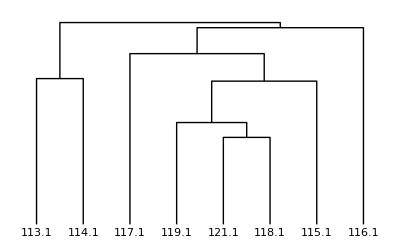

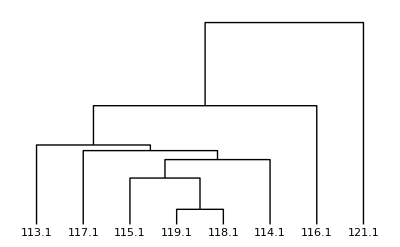

```mathematica
DendrogramPlot[sanitisedPeptides1ᵀ,LeafLabels->heads[[11;;18]]]
DendrogramPlot[sanitisedPeptides2ᵀ,LeafLabels->heads[[11;;18]]]
```

Clusters after normalisation

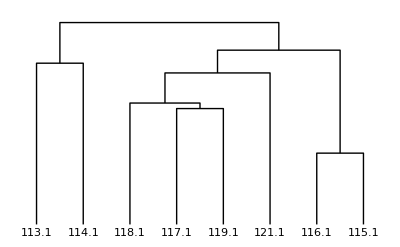

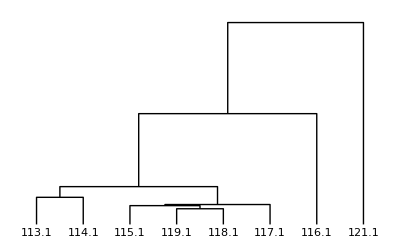

```mathematica
DendrogramPlot[normalisedPeptides1ᵀ,LeafLabels->heads[[11;;18]]]
DendrogramPlot[normalisedPeptides2ᵀ,LeafLabels->heads[[11;;18]]]
```

### PCA

```mathematica
pca1=PrincipalComponents[normalisedPeptides1ᵀ];
pca2=PrincipalComponents[normalisedPeptides2ᵀ];
```

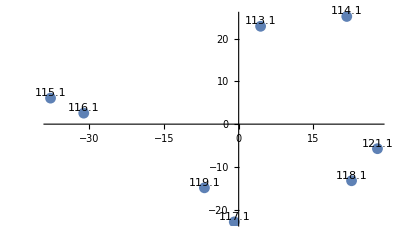

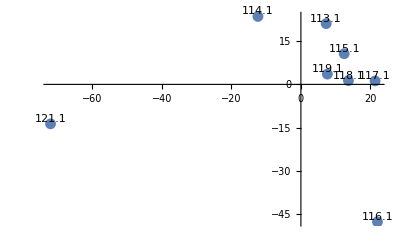

```mathematica
pcaPlot1=ListPlot[pca1[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
pcaPlot2=ListPlot[pca2[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
```

```mathematica
Export["Porto_PCA_iTRAQ1.pdf",pcaPlot1]
Export["Porto_PCA_iTRAQ2.pdf",pcaPlot2]
```

## Protein investigation

### Import data

```mathematica
proteins1=Import["13212_iTRAQ1-quants.xls"][[2]];
proteins2=Import["13211_iTRAQ2-quants.xls"][[2]];
proteins1//Dimensions
proteins2//Dimensions
```

{464,66}

{631,66}

### Collect intersecting proteins

```mathematica
acValues1=proteins1[[3;;All,1]];
acValues2=proteins2[[3;;All,1]];
```

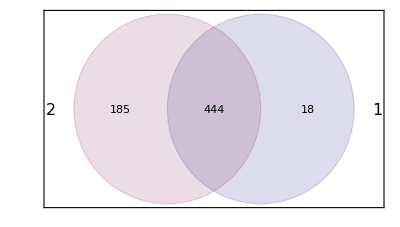

```mathematica
VennDiagram[{acValues1,acValues2}]
```

```mathematica
sharedProteins=Intersection[acValues1,acValues2];
Dimensions[sharedProteins]
```

{444}

### PCA of intersecting proteins

```mathematica
proteinIntensities1=Map[Association@@Thread[acValues1->#]&,proteins1[[3;;All,27;;34]]ᵀ]; (*Isotopic correction, Median correction, Log Values*)
proteinIntensities2=Map[Association@@Thread[acValues2->#]&,proteins2[[3;;All,27;;34]]ᵀ];
```

```mathematica
sharedProteinIntensities=Table[f[[All,Key[sharedProteins[[k]]]]],{k,Length[sharedProteins]},{f,{proteinIntensities1,proteinIntensities2}}];
sharedProteinIntensities=Flatten[Transpose[sharedProteinIntensities,{3,1,2}],1]ᵀ;
```

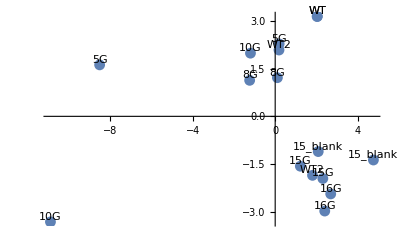

```mathematica
heads={"WT","WT2","15G","15G","16G","16G","15_blank","15_blank","WT","WT2","5G","5G","8G","8G","10G","10G"};
pca=PrincipalComponents[sharedProteinIntensitiesᵀ];
ListPlot[pca[[All,1;;2]],Epilog->Table[Text[heads[[i]],pca[[i,{1,2}]],{0,-2}],{i,16}],PlotRangePadding->Scaled[.1],PlotRange->Full]
```

Not meshing properly based on WT2 positioning.

## Normalising by median correction

```mathematica
normalised=Association@@Table[
l=Log[dat⟦All,Key[k]⟧];
p=Flatten[Position[l,-∞]];
min=Sanitized[Min][N[l]];
l=N[l]/.-∞->min;
{L,M,R}=Quantile[l,{0.45,0.5,0.55}];
n=(l-M)/(R-L);
n⟦p⟧=-∞;
k->n,

{k,labels}];
```

## New section

#### Median Correction

```mathematica
dat=Map[Association@@Thread[heads->#]&,fdrData];
dat2=Map[Association@@Thread[heads->#]&,fdrdat2];
```

```mathematica
labels=Range[114.1,119.1,1]
labels2=Append[Range[113.1,119.1],121.1]
```

{114.1,115.1,116.1,117.1,118.1,119.1}

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

```mathematica
{newdat,predat,predat2}={dat,dat,dat2};
```

### iTRAQ 1

#### Incorrect way

```mathematica
normalised=Association@@Table[
l=Log[dat⟦All,Key[k]⟧];
p=Flatten[Position[l,-∞]];
min=Sanitized[Min][N[l]];
l=N[l]/.-∞->min;
andrew=Sort[l][[Length[p];;All]];(**)
{L,M,R}=Quantile[andrew,{0.45,0.5,0.55}];(**)
n=(l-M)/(R-L);
n⟦p⟧=-∞;
k->n,

{k,labels}];
```

```mathematica
Dimensions[Values@normalised]
```

{6,8781}

```mathematica
Do[newdat⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,labels}]
```

#### Correct way

```mathematica
Dimensions[Values@normalised]
```

{6,8781}

```mathematica
Do[dat⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,labels}]
```

#### Visualise

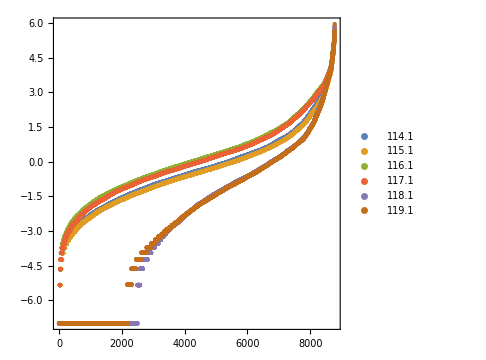

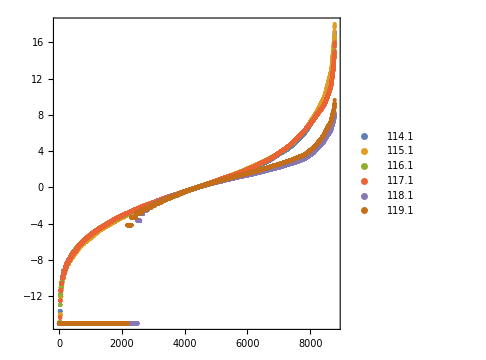

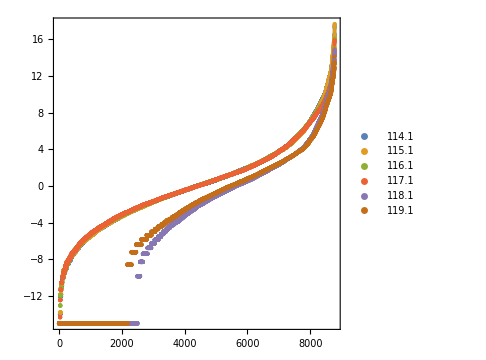

```mathematica
ListPlot[Evaluate@Table[Sort[N[Log[predat⟦All,Key[k]⟧/.(0|0.->Exp[-7.])]]],{k,labels}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->labels,PlotStyle->PointSize[Medium]]
ListPlot[Evaluate@Table[Sort[N[Log[dat⟦All,Key[k]⟧/.(0|0.->Exp[-15.])]]],{k,labels}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->labels,PlotStyle->PointSize[Medium]]
ListPlot[Evaluate@Table[Sort[N[Log[newdat⟦All,Key[k]⟧/.(0|0.->Exp[-15.])]]],{k,labels}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->labels,PlotStyle->PointSize[Medium]]
```

### iTRAQ 2 normalisation

```mathematica
normalised=Association@@Table[
l=Log[dat2⟦All,Key[k]⟧];
p=Flatten[Position[l,-∞]];
min=Sanitized[Min][N[l]];
l=N[l]/.-∞->min;
{L,M,R}=Quantile[l,{0.45,0.5,0.55}];
n=(l-M)/(R-L);
n⟦p⟧=-∞;
k->n,

{k,labels2}];
```

```mathematica
Dimensions[Values@normalised]
```

{8,4191}

```mathematica
Do[dat2⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,labels2}]
```

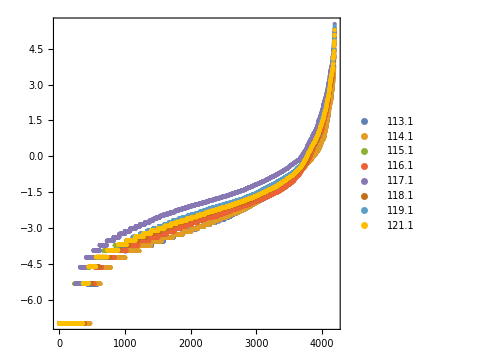

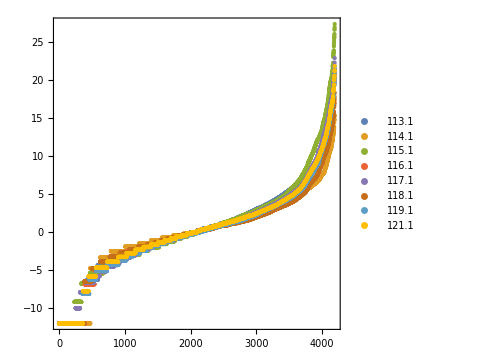

```mathematica
ListPlot[Evaluate@Table[Sort[N[Log[predat2⟦All,Key[k]⟧/.(0|0.->Exp[-7.])]]],{k,labels2}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->labels2,PlotStyle->PointSize[Medium]]
ListPlot[Evaluate@Table[Sort[N[Log[dat2⟦All,Key[k]⟧/.(0|0.->Exp[-12.])]]],{k,labels2}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->labels2,PlotStyle->PointSize[Medium]]
```